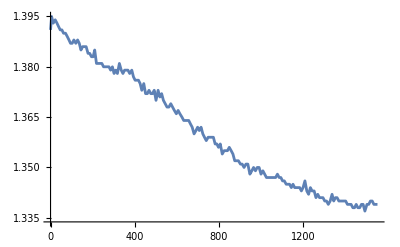

```mathematica
data = Import["C:\\Users\\saran\\ProgrammingFiles\\MagnetoOpticalTrapping-Analysis\\Modified-Data\\GaussianData-ObservationNo1.txt","CSV"];


p1 = ListLinePlot[data]
```

```mathematica
model =OFFSET+ A*(1+Exp[-t/T]);
```

```mathematica
Print[FindFit[data,model,{OFFSET, A,T},{t}]];
```

{OFFSET→1.20008,A→0.0975076,T→1635.04}

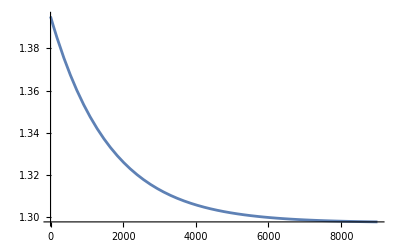

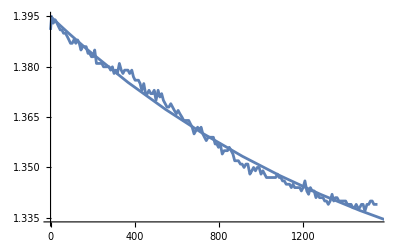

```mathematica
p2 = Plot[1.2+0.0975076*(1+Exp[-t/1635.04]),{t,0,9000}]

Show[p1,p2]
```